# KL Distance Analysis

## Functional form of B

```mathematica
params={7.52,1.4,5.2};
```

#### B

(s1+ⅇ^(-s3 (-5.+t)^2) (-s1+s2))^2

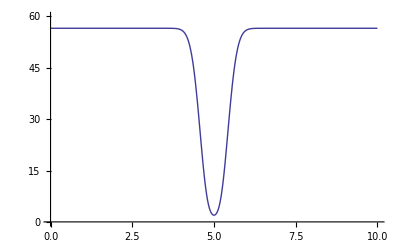

```mathematica
Bxx[t_,{s1_,s2_,s3_}]=(s1+(s2-s1)*Exp[-s3*(t-5.)^2])^2
Plot[Bxx[t,params],{t,0,10},PlotRange->{{0,10},{0,60}}]
```

### dB/ds_1

2 (1-ⅇ^(-s3 (-5.+t)^2)) (s1+ⅇ^(-s3 (-5.+t)^2) (-s1+s2))

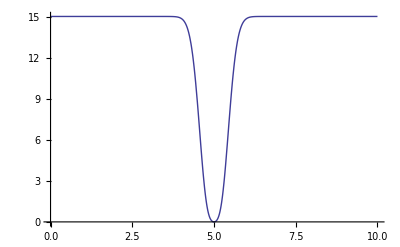

```mathematica
Bxxds1[t_,{s1_,s2_,s3_}]=D[Bxx[t,s1,s2,s3],s1]
Plot[Bxxds1[t,params],{t,0,10},PlotRange->All]
```

### dB/ds_2

2 ⅇ^(-s3 (-5.+t)^2) (s1+ⅇ^(-s3 (-5.+t)^2) (-s1+s2))

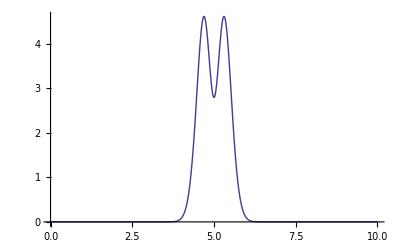

```mathematica
Bxxds2[t_,{s1_,s2_,s3_}]=D[Bxx[t,s1,s2,s3],s2]
Plot[Bxxds2[t,params],{t,0,10},PlotRange->All]
```

### dB/ds_3

-2 ⅇ^(-s3 (-5.+t)^2) (-s1+s2) (s1+ⅇ^(-s3 (-5.+t)^2) (-s1+s2)) (-5.+t)^2

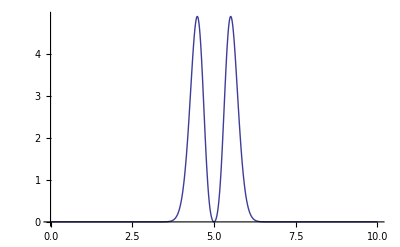

```mathematica
Bxxds3[t_,{s1_,s2_,s3_}]=D[Bxx[t,s1,s2,s3],s3]
Plot[Bxxds3[t,params],{t,0,10},PlotRange->All]
```

## Simulation Data

```mathematica
data=Import["/mnt/heimdall/git/TwoDimTubes/2WellTubes-T0.15-pos0001000.dat","Table"];
```

```mathematica
timedata=Table[i,{i,0,10,0.0005}];
```

### dD_kl/dm

I-Iou= -9.28544

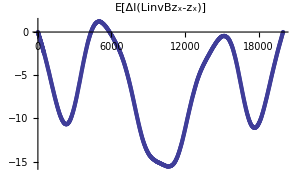

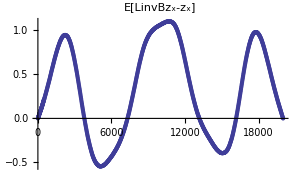

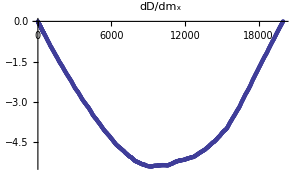

```mathematica
Print["I-Iou= "<>ToString[data[[1,9]]]]
ListPlot[data[[All,8]],PlotRange->All,MaxPlotPoints->1000,ImageSize->300,PlotLabel->"E[ΔI(LinvBz_x-z_x)]"]
ListPlot[data[[All,10]],PlotRange->All,MaxPlotPoints->1000,ImageSize->300,PlotLabel->"E[LinvBz_x-z_x]"]
ListPlot[data[[All,8+0]]-data[[All,8+1]]*data[[All,8+2]],PlotRange->All,MaxPlotPoints->1000,PlotLabel->"dD/dm_x"]
```

I-Iou= -9.28544

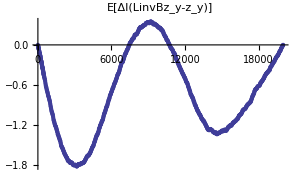

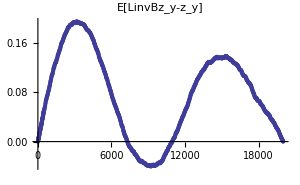

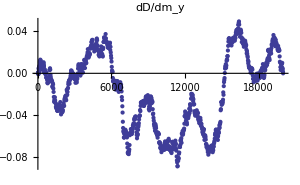

```mathematica
Print["I-Iou= "<>ToString[data[[1,12]]]]
ListPlot[data[[All,11]],PlotRange->All,MaxPlotPoints->1000,ImageSize->300,PlotLabel->"E[ΔI(LinvBz_y-z_y)]"]
ListPlot[data[[All,13]],PlotRange->All,MaxPlotPoints->1000,ImageSize->300,PlotLabel->"E[LinvBz_y-z_y]"]
ListPlot[data[[All,11+0]]-data[[All,11+1]]*data[[All,11+2]],PlotRange->All,MaxPlotPoints->1000,PlotLabel->"dD/dm_y"]
```

### dD_kl/dB_xx

I-Iou= -9.28544

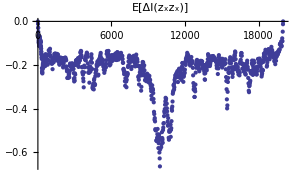

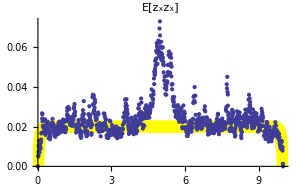

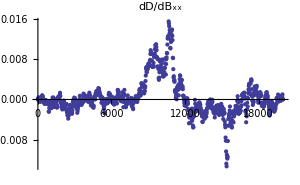

```mathematica
Print["I-Iou= "<>ToString[data[[1,15]]]]
ListPlot[data[[All,14]],PlotRange->All,MaxPlotPoints->1000,ImageSize->300,PlotLabel->"E[ΔI(z_xz_x)]"]
Show[Plot[2 ϵ/A Sinh[A t] Sinh[A (T-t)]/Sinh[A T]/.{A->params[[1]],ϵ->0.15,T->10},{t,0,10},PlotRange->All,PlotStyle->{Thickness[.03],Yellow},PlotLabel->"E[z_xz_x]"],ListPlot[Transpose[{timedata,data[[All,16]]}],PlotRange->All,MaxPlotPoints->1000,ImageSize->300]]
ListPlot[-data[[All,14+0]]+data[[All,14+1]]*data[[All,14+2]],PlotRange->All,MaxPlotPoints->1000,PlotLabel->"dD/dB_xx"]
```

dD_KL/dσ_2=∫dD/dB_xx dB_xx/dσ_2 du

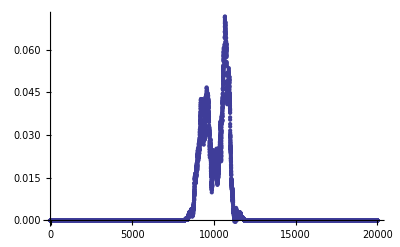

```mathematica
ListPlot[Table[Bxxds2[timedata[[i]],params],{i,1,Length[timedata]}]*(-data[[All,14+0]]+data[[All,14+1]]*data[[All,14+2]]),PlotRange->All]
```

```mathematica
Table[Bxxds2[timedata[[i]],params],{i,1,Length[timedata]}].(-data[[All,14+0]]+data[[All,14+1]]*data[[All,14+2]])
```

75.752

```mathematica
Table[Bxxds3[timedata[[i]],params],{i,1,Length[timedata]}].(-data[[All,14+0]]+data[[All,14+1]]*data[[All,14+2]])
```

53.7365

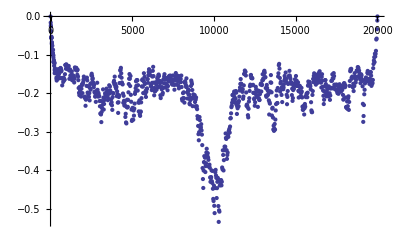

```mathematica
ListPlot[data[[All,1jj]],PlotRange->All,MaxPlotPoints->1000]
```